```mathematica
ListSigmaOfΣn[Σn_]:=Join[Σn/@domain[Σn],ListComplement[ListSigmaAll,Σn/@domain[Σn]]]
```

```mathematica
ListSigmaOfΣn[ΣnTETXISO]
ListSigmaOfΣn[ΣnTETCUBE]
```

{TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE}

{TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG}

```mathematica
SigmaPairsMatrix[Σn_,dim_]:=Table[{Take[ListSigmaOfΣn[Σn],dim][[j]],Take[ListSigmaOfΣn[Σn],dim][[k]]},{j,dim},{k,dim}];
```

#### Example

```mathematica
MatrixForm[SigmaPairsMatrix[ΣnTETCUBE,6]]
```

((TRIV
TRIV) | (TRIV
MONO) | (TRIV
ORTH) | (TRIV
TET) | (TRIV
CUBE) | (TRIV
ISO)
(MONO
TRIV) | (MONO
MONO) | (MONO
ORTH) | (MONO
TET) | (MONO
CUBE) | (MONO
ISO)
(ORTH
TRIV) | (ORTH
MONO) | (ORTH
ORTH) | (ORTH
TET) | (ORTH
CUBE) | (ORTH
ISO)
(TET
TRIV) | (TET
MONO) | (TET
ORTH) | (TET
TET) | (TET
CUBE) | (TET
ISO)
(CUBE
TRIV) | (CUBE
MONO) | (CUBE
ORTH) | (CUBE
TET) | (CUBE
CUBE) | (CUBE
ISO)
(ISO
TRIV) | (ISO
MONO) | (ISO
ORTH) | (ISO
TET) | (ISO
CUBE) | (ISO
ISO))

#### Here is how the Map function works .

```mathematica
MatrixForm[Map[#[[1]]+#[[2]]&,SigmaPairsMatrix[ΣnTETCUBE,6],{2}]]
```

(2 TRIV | MONO+TRIV | ORTH+TRIV | TET+TRIV | CUBE+TRIV | ISO+TRIV
MONO+TRIV | 2 MONO | MONO+ORTH | MONO+TET | CUBE+MONO | ISO+MONO
ORTH+TRIV | MONO+ORTH | 2 ORTH | ORTH+TET | CUBE+ORTH | ISO+ORTH
TET+TRIV | MONO+TET | ORTH+TET | 2 TET | CUBE+TET | ISO+TET
CUBE+TRIV | CUBE+MONO | CUBE+ORTH | CUBE+TET | 2 CUBE | CUBE+ISO
ISO+TRIV | ISO+MONO | ISO+ORTH | ISO+TET | CUBE+ISO | 2 ISO)

```mathematica
InternodalAngles[Tmat_,Σn_,nm_,dim_]:=Map[Round[AngleMatrix[SmatOfΣ[#[[1]],Tmat,Σn,nm],SmatOfΣ[#[[2]],Tmat,Σn,nm]]/Degree,.01]&,SigmaPairsMatrix[Σn,dim],{2}];
```

#### Examples

```mathematica
nm=nm2;Σn=ΣnTETXISO;
MatrixNote[Tmat]
TextNodeMode[nm]
ListSigmaOfΣn[Σn]
MatrixForm[InternodalAngles[Tmat,Σn,nm,6]]
MatrixForm[InternodalAngles[Tmat,Σn,nm,8]]
```

T is Brown

Node mode nm2: Closest to Tmat

{TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE}

(0. | 3.77 | 6.42 | 7.86 | 18.62 | 26.04
3.77 | 0. | 5.22 | 6.97 | 19.02 | 25.78
6.42 | 5.22 | 0. | 4.82 | 18.31 | 25.29
7.86 | 6.97 | 4.82 | 0. | 17.92 | 24.9
18.62 | 19.02 | 18.31 | 17.92 | 0. | 18.54
26.04 | 25.78 | 25.29 | 24.9 | 18.54 | 0.)

(0. | 3.77 | 6.42 | 7.86 | 18.62 | 26.04 | 16.23 | 21.12
3.77 | 0. | 5.22 | 6.97 | 19.02 | 25.78 | 16.47 | 20.95
6.42 | 5.22 | 0. | 4.82 | 18.31 | 25.29 | 18.82 | 20.36
7.86 | 6.97 | 4.82 | 0. | 17.92 | 24.9 | 19.79 | 19.76
18.62 | 19.02 | 18.31 | 17.92 | 0. | 18.54 | 20.68 | 13.21
26.04 | 25.78 | 25.29 | 24.9 | 18.54 | 0. | 20.64 | 15.59
16.23 | 16.47 | 18.82 | 19.79 | 20.68 | 20.64 | 0. | 22.4
21.12 | 20.95 | 20.36 | 19.76 | 13.21 | 15.59 | 22.4 | 0.)

```mathematica
rrow[i_,Tmat_,Σn_,nm_,dim_]:=Join[{Take[ListSigmaOfΣn[Σn],dim][[i]]},InternodalAngles[Tmat,Σn,nm,dim][[i]]];
rrow[0,Tmat_,Σn_,nm_,dim_]:=Join[{""},Take[ListSigmaOfΣn[Σn],dim]];
```

#### Examples

```mathematica
Σn=ΣnTETCUBE;dim=8;
rrow[0,Tmat,Σn,nm2,dim]
rrow[3,Tmat,Σn,nm2,dim]
```

{,TRIV,MONO,ORTH,TET,CUBE,ISO,XISO,TRIG}

{ORTH,6.42,5.22,0.,4.82,20.36,25.29,18.31,18.82}

```mathematica
dim=6;WantNumbers="WantNumbers";
MatrixNote[Tmat]
TextNodeMode[nm]
MatrixForm[Table[rrow[i,Tmat,Σn,nm,dim],{i,0,dim}]]
```

T is Brown

Node mode nm2: Closest to Tmat

( | TRIV | MONO | ORTH | TET | CUBE | ISO
TRIV | 0. | 3.77 | 6.42 | 7.86 | 21.12 | 26.04
MONO | 3.77 | 0. | 5.22 | 6.97 | 20.95 | 25.78
ORTH | 6.42 | 5.22 | 0. | 4.82 | 20.36 | 25.29
TET | 7.86 | 6.97 | 4.82 | 0. | 19.76 | 24.9
CUBE | 21.12 | 20.95 | 20.36 | 19.76 | 0. | 15.59
ISO | 26.04 | 25.78 | 25.29 | 24.9 | 15.59 | 0.)

```mathematica
gg[i_,j_,Tmat_,Σn_,nm_,dim_]:=InternodalAngles[Tmat,Σn,nm,dim][[i,j]];
```

#### Example

```mathematica
MatrixNote[Tmat]
TextNodeMode[nm]
gg[4,5,Tmat,ΣnTETXISO,nm,6]
```

T is Brown

Node mode nm2: Closest to Tmat

17.92

```mathematica
Sort[Flatten[InternodalAngles[Tmat,Σn,nm,8]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,3.77,3.77,4.82,4.82,5.22,5.22,6.42,6.42,6.97,6.97,7.86,7.86,13.21,13.21,15.59,15.59,16.23,16.23,16.47,16.47,17.92,17.92,18.31,18.31,18.54,18.54,18.62,18.62,18.82,18.82,19.02,19.02,19.76,19.76,19.79,19.79,20.36,20.36,20.64,20.64,20.68,20.68,20.95,20.95,21.12,21.12,22.4,22.4,24.9,24.9,25.29,25.29,25.78,25.78,26.04,26.04}

```mathematica
ForScaling:=Max[Flatten[InternodalAngles[Tmat,ΣnTETXISO,nm2,8]]]; (* May need to change *)
```

```mathematica
ForScaling
```

26.04

```mathematica
PreCheckerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_]:={Table[{FaceForm[ColorData["TemperatureMap"][gg[i,j,Tmat,Σn,nm,dim]/ForScaling]],Cuboid[{i-.5,-j-.5},{i+.5,-j+.5}]},{i,dim},{j,dim}],
If[WantNumbers=="WantNumbers",Table[Text[Style[Round[gg[i,j,Tmat,Σn,nm,dim],.1],13],{i,-j}],{i,dim},{j,dim}]]};
```

```mathematica
hw=1.5;fontsize=15;WantRound="NoWantRound";increment=2;offset=2.5;
Show[legends[Range[0,24,4],22,SubscriptBox[Style["α",20],Style["MONO",11]]//DisplayForm,hw,fontsize,increment,offset],ImageSize->100,PlotRange->All]
```

-Graphics-

```mathematica
Checkerboard[Tmat_,Σn_,nm_,dim_,ForScaling_,WantNumbers_,WantLegends_]:=Graphics[{
Text[#,{Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]],0}]&/@Take[ListSigmaOfΣn[Σn],dim],
Text[#,{-.2,-Position[Take[ListSigmaOfΣn[Σn],dim],#][[1,1]]}]&/@Take[ListSigmaOfΣn[Σn],dim],PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers],
If[WantLegends=="WantLegends",Inset[legends[Range[0,5+ForScaling,5],ForScaling,"",hww,fontsize,increment,offset],{3+dim,-3},Center,1.8] ]},ImageSize->If[WantLegends=="WantLegends",510,350]](* legends *)
```

```mathematica
nm=nm4;Σn=ΣnTETXISO;dim=6;WantNumbers="WantNumbers"
PreCheckerboard[Tmat,Σn,nm,dim,ForScaling,WantNumbers]
```

WantNumbers

{{{{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{0.5,-1.5},{1.5,-0.5}]},{FaceForm[RGBColor[0.6628227096774194, 0.736521405529954, 0.9670276313364055]],Cuboid[{0.5,-2.5},{1.5,-1.5}]},{FaceForm[RGBColor[0.9920112165898618, 0.9909644470046083, 0.7820583456221196]],Cuboid[{0.5,-3.5},{1.5,-2.5}]},{FaceForm[RGBColor[0.9719597741935484, 0.9170758755760366, 0.34556944700460807]],Cuboid[{0.5,-4.5},{1.5,-3.5}]},{FaceForm[RGBColor[0.9712862258064516, 0.9148038387096773, 0.3429528387096773]],Cuboid[{0.5,-5.5},{1.5,-4.5}]},{FaceForm[RGBColor[0.817319, 0.134127, 0.164218]],Cuboid[{0.5,-6.5},{1.5,-5.5}]}},{{FaceForm[RGBColor[0.6628227096774194, 0.736521405529954, 0.9670276313364055]],Cuboid[{1.5,-1.5},{2.5,-0.5}]},{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{1.5,-2.5},{2.5,-1.5}]},{FaceForm[RGBColor[0.9817338294930875, 0.9858977004608296, 0.9158040414746543]],Cuboid[{1.5,-3.5},{2.5,-2.5}]},{FaceForm[RGBColor[0.992515806451613, 0.9864003917050692, 0.4267699032258059]],Cuboid[{1.5,-4.5},{2.5,-3.5}]},{FaceForm[RGBColor[0.9919978387096774, 0.9846689723502303, 0.4234135437788017]],Cuboid[{1.5,-5.5},{2.5,-4.5}]},{FaceForm[RGBColor[0.8332232580645161, 0.2563740967741934, 0.17944793548387095]],Cuboid[{1.5,-6.5},{2.5,-5.5}]}},{{FaceForm[RGBColor[0.9920112165898618, 0.9909644470046083, 0.7820583456221196]],Cuboid[{2.5,-1.5},{3.5,-0.5}]},{FaceForm[RGBColor[0.9817338294930875, 0.9858977004608296, 0.9158040414746543]],Cuboid[{2.5,-2.5},{3.5,-1.5}]},{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{2.5,-3.5},{3.5,-2.5}]},{FaceForm[RGBColor[0.9544704838709677, 0.9655647419354839, 0.9619537741935484]],Cuboid[{2.5,-4.5},{3.5,-3.5}]},{FaceForm[RGBColor[0.9555878341013825, 0.9663980599078341, 0.9600623917050691]],Cuboid[{2.5,-5.5},{3.5,-4.5}]},{FaceForm[RGBColor[0.9014819032258065, 0.6455341566820275, 0.23950642396313362]],Cuboid[{2.5,-6.5},{3.5,-5.5}]}},{{FaceForm[RGBColor[0.9719597741935484, 0.9170758755760366, 0.34556944700460807]],Cuboid[{3.5,-1.5},{4.5,-0.5}]},{FaceForm[RGBColor[0.992515806451613, 0.9864003917050692, 0.4267699032258059]],Cuboid[{3.5,-2.5},{4.5,-1.5}]},{FaceForm[RGBColor[0.9544704838709677, 0.9655647419354839, 0.9619537741935484]],Cuboid[{3.5,-3.5},{4.5,-2.5}]},{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{3.5,-4.5},{4.5,-3.5}]},{FaceForm[RGBColor[0.24533211059907836, 0.3751899815668203, 0.9372826728110599]],Cuboid[{3.5,-5.5},{4.5,-4.5}]},{FaceForm[RGBColor[0.9721281612903225, 0.9176438847926266, 0.3462235990783409]],Cuboid[{3.5,-6.5},{4.5,-5.5}]}},{{FaceForm[RGBColor[0.9712862258064516, 0.9148038387096773, 0.3429528387096773]],Cuboid[{4.5,-1.5},{5.5,-0.5}]},{FaceForm[RGBColor[0.9919978387096774, 0.9846689723502303, 0.4234135437788017]],Cuboid[{4.5,-2.5},{5.5,-1.5}]},{FaceForm[RGBColor[0.9555878341013825, 0.9663980599078341, 0.9600623917050691]],Cuboid[{4.5,-3.5},{5.5,-2.5}]},{FaceForm[RGBColor[0.24533211059907836, 0.3751899815668203, 0.9372826728110599]],Cuboid[{4.5,-4.5},{5.5,-3.5}]},{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{4.5,-5.5},{5.5,-4.5}]},{FaceForm[RGBColor[0.9726333225806452, 0.9193479124423963, 0.34818605529953917]],Cuboid[{4.5,-6.5},{5.5,-5.5}]}},{{FaceForm[RGBColor[0.817319, 0.134127, 0.164218]],Cuboid[{5.5,-1.5},{6.5,-0.5}]},{FaceForm[RGBColor[0.8332232580645161, 0.2563740967741934, 0.17944793548387095]],Cuboid[{5.5,-2.5},{6.5,-1.5}]},{FaceForm[RGBColor[0.9014819032258065, 0.6455341566820275, 0.23950642396313362]],Cuboid[{5.5,-3.5},{6.5,-2.5}]},{FaceForm[RGBColor[0.9721281612903225, 0.9176438847926266, 0.3462235990783409]],Cuboid[{5.5,-4.5},{6.5,-3.5}]},{FaceForm[RGBColor[0.9726333225806452, 0.9193479124423963, 0.34818605529953917]],Cuboid[{5.5,-5.5},{6.5,-4.5}]},{FaceForm[RGBColor[0.178927, 0.305394, 0.933501]],Cuboid[{5.5,-6.5},{6.5,-5.5}]}}},{{Text[0.,{1,-1}],Text[6.8,{1,-2}],Text[14.6,{1,-3}],Text[18.6,{1,-4}],Text[18.6,{1,-5}],Text[26.,{1,-6}]},{Text[6.8,{2,-1}],Text[0.,{2,-2}],Text[12.9,{2,-3}],Text[17.4,{2,-4}],Text[17.4,{2,-5}],Text[25.2,{2,-6}]},{Text[14.6,{3,-1}],Text[12.9,{3,-2}],Text[0.,{3,-3}],Text[11.7,{3,-4}],Text[11.7,{3,-5}],Text[21.8,{3,-6}]},{Text[18.6,{4,-1}],Text[17.4,{4,-2}],Text[11.7,{4,-3}],Text[0.,{4,-4}],Text[1.1,{4,-5}],Text[18.6,{4,-6}]},{Text[18.6,{5,-1}],Text[17.4,{5,-2}],Text[11.7,{5,-3}],Text[1.1,{5,-4}],Text[0.,{5,-5}],Text[18.5,{5,-6}]},{Text[26.,{6,-1}],Text[25.2,{6,-2}],Text[21.8,{6,-3}],Text[18.6,{6,-4}],Text[18.5,{6,-5}],Text[0.,{6,-6}]}}}

#### Examples

```mathematica
ForScaling
```

26.04

#### For legends. The setting increment = n prints every n^th contour label.

```mathematica
hww=1.2;fontsize=12;increment=1;offset=2.5; WantRound=="NoWantRound";
```

T is Brown

Node mode nm4: P(T,𝒱_Σ(U))

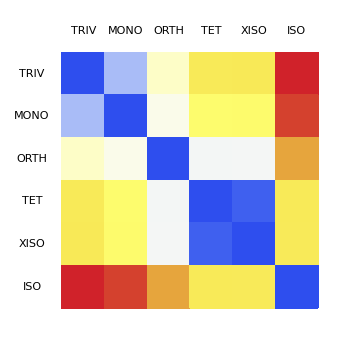

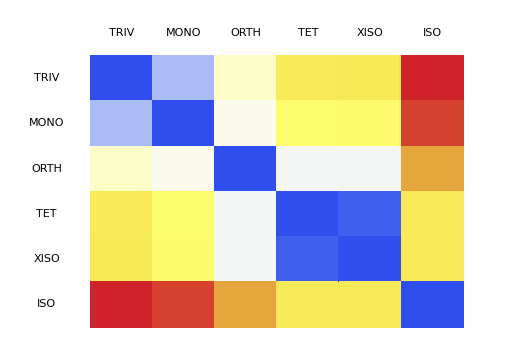
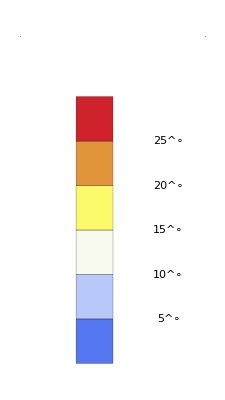

```mathematica
nm=nm4;Σn=ΣnTETXISO;dim=6;
MatrixNote[Tmat]
TextNodeMode[nm]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
```

T is Brown

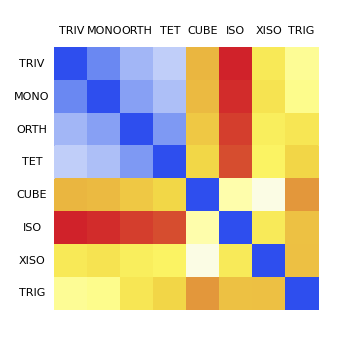

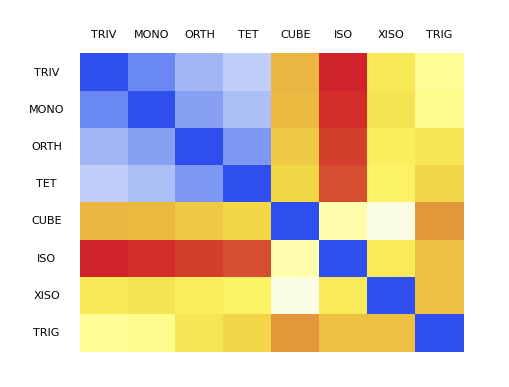
-Graphics-
-Graphics-

T is Brown

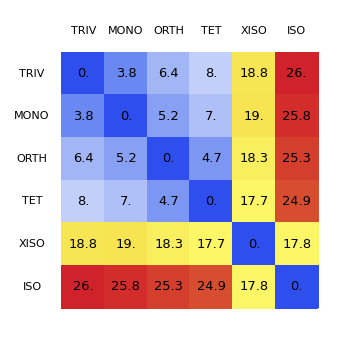

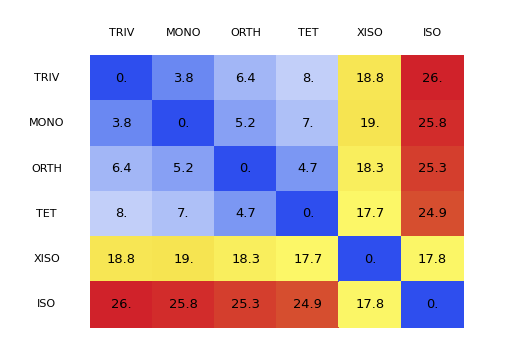
-Graphics-
-Graphics-

```mathematica
nm=nm2;Σn=ΣnTETCUBE;dim=8;
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"NoWantNumbers","WantLegends"]
Print[" "];
nm=nm3;Σn=ΣnTETXISO;dim=6;  (* dim must be nMax[Σn] for nm3 *)
MatrixNote[Tmat]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","NoWantLegends"]
Checkerboard[Tmat,Σn,nm,dim,ForScaling,"WantNumbers","WantLegends"]
Print[" "];
```